0

/home/zchen96/Projects/TimeIntegrator/MMACodes/plots_shift_0./0.005/external_force_h_0.005_sin_pow_10

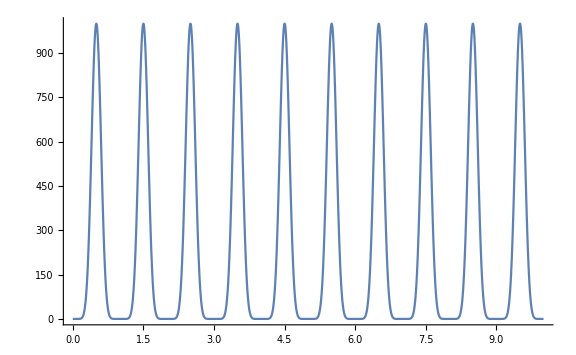

/home/zchen96/Projects/TimeIntegrator/MMACodes/plots_shift_0./0.005/external_force_h_0.005_sin_pow_10_force.png

```mathematica
(*setup information*)
h= 1 /200; 
λ=2000;
a0= 1; 
c= 0;
totalTime = 10;
numSteps = totalTime / h;
pow =10;
epsilon = 0
varC[t_] = 1000*Sin[Pi t + epsilon]^pow;
With[{dirname=FileNameJoin[{NotebookDirectory[],"plots_shift_" <> ToString[epsilon//N]<>"/"<>ToString[h//N]}]},Switch[FileType[dirname],None,CreateDirectory[dirname] (*create dir*),Directory,Null (*do nothing*),File,Print["File with same name already exists!!"] (*error!*)]]
filePrefex = FileNameJoin[{NotebookDirectory[],"plots_shift_" <> ToString[epsilon//N]<>"/"<>ToString[h//N]}]<> "/external_force_h_" <> ToString[h//N] <> "_sin_pow_" <> ToString[pow]
forcePlot = Plot[varC[t], {t, 0, totalTime}, PlotRange->All, ImageSize->Large]
Export[filePrefex <> "_force.png", forcePlot]
(*exact solution for changed c*)
```

InterpolatingFunction[…][t]

Cos[20 √5 t]

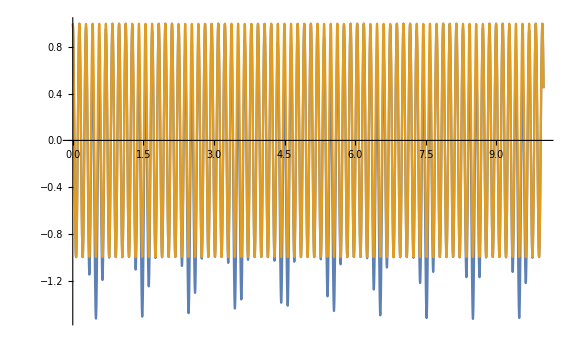

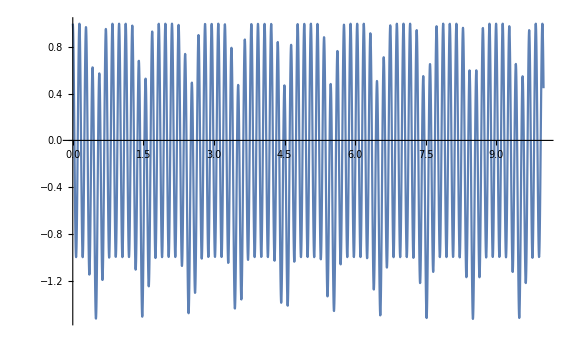

```mathematica
theoSol = NDSolve[{f''[t]+λ f[t]+varC[t]==0,f[0]==a0,f'[0]==0},f[t],{t, 0, totalTime},MaxStepFraction-> 1/100];
theoα[t_] = (f[t]/.theoSol[[1]]) // FullSimplify
oldα[t_] = (a0 + c / λ) Cos[Sqrt[λ]t] - c / λ
Plot[{theoα[t], oldα[t]}, {t, 0, totalTime}, ImageSize->Large]
Plot[{theoα[t]}, {t, 0, totalTime}, ImageSize->Large]
```

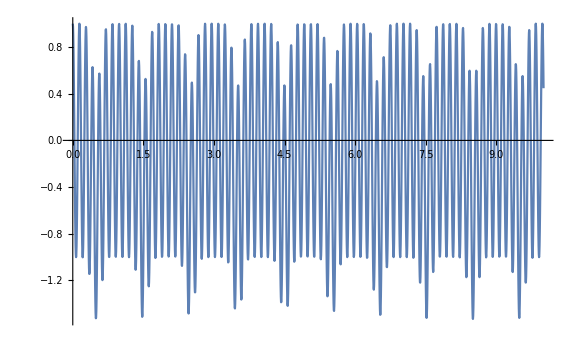

```mathematica
theoList = Table[{n *h, theoα[n* h]}, {n, 0, numSteps}];
ListLinePlot[theoList, PlotRange->All, ImageSize->Large]
```

```mathematica
N
```

N

```mathematica
(*Implicit Euler*)
```

```mathematica
IEM = {{1, -h},{λ h, 1}};
IEw1[n_]= {0,-h varC[n h]};
IEA = Inverse[IEM];
 IEw[n_]= IEA.IEw1[n];
```

```mathematica
IEα = {a0};
IEβ = {0};
timeList = {0};
IEtimeα = {{0, a0}}
For[i=1,i≤numSteps,
a =(IEA[[1,1]] IEα[[i]] + IEA[[1,2]] IEβ[[i]] + IEw[i][[1]])// N;
 b=(IEA[[2,1]] IEα[[i]] + IEA[[2,2]] IEβ[[i]] + IEw[i][[2]])// N;
AppendTo[IEα, a];
AppendTo[IEβ, b];
AppendTo[timeList, i * h];
AppendTo[IEtimeα, {i * h, a}];
i++] ;
```

{{0,1}}

```mathematica
(*Newmark-β*)
NMM = {{1 + h^2 λ β, 0},{λ h / 2, 1}};
NMw1[n_] = {-h^2varC[n h] / 2, - h varC[n h]};
NMM1 ={{1 - h ^2 λ(1/2 - β), h}, {-λ h / 2, 1}}
NMA = Inverse[NMM].NMM1;
NMw[n_] = Inverse[NMM].NMw1[n];
```

{{1+1/20 (-1/2+β),1/200},{-5,1}}

```mathematica
NMα = {a0};
NMβ = {0};
NMtimeα = {{0, a0}};
For[i=1,i≤numSteps,
a =(NMA[[1,1]] NMα[[i]] + NMA[[1,2]] NMβ[[i]] + NMw[i][[1]])/.{β-> 1/4}// N;
 b=(NMA[[2,1]] NMα[[i]] + NMA[[2,2]] NMβ[[i]] + NMw[i][[2]])/.{β-> 1/4}// N;
AppendTo[NMα, a];
AppendTo[NMβ, b];
AppendTo[NMtimeα, {i * h, a}];
i++];
```

```mathematica
(*BDF2*)
BDF2M = {{1, -2h/3}, {2h λ/3, 1}};
BDF2M1 = {{4/3, 0}, {0, 4/3}};
BDF2M2 = {{-1/3, 0}, {0, -1/3}};
BDF2w1[n_] = {0, -2h varC[n * h]/3};
BDF2A1 = Inverse[BDF2M].BDF2M1
BDF2A2 = Inverse[BDF2M].BDF2M2;
BDF2w[n_] = Inverse[BDF2M].BDF2w1[n]
```

{{30/23,1/230},{-200/23,30/23}}

{-1/92 Sin[(n π)/200]^10,-75/23 Sin[(n π)/200]^10}

```mathematica
BDF2α = {a0, IEα[[2]]};
BDF2β = {0, IEβ[[2]]};
BDF2timeα = {{0, a0}, {h, IEα[[2]]}};
For[i=2,i≤numSteps,
a =(BDF2A1[[1,1]] BDF2α[[i]] + BDF2A1[[1,2]] BDF2β[[i]] + BDF2A2[[1,1]] BDF2α[[i-1]] + BDF2A2[[1,2]] BDF2β[[i - 1]] + BDF2w[i][[1]])// N;
 b=(BDF2A1[[2,1]] BDF2α[[i]] + BDF2A1[[2,2]] BDF2β[[i]] + BDF2A2[[2,1]] BDF2α[[i-1]] + BDF2A2[[2,2]] BDF2β[[i - 1]] + BDF2w[i][[2]])// N;
AppendTo[BDF2α, a];
AppendTo[BDF2β, b];
AppendTo[BDF2timeα, {i * h, a}];
i++];
```

```mathematica
Print[BDF2α]
```

{1,0.952381,0.874741,0.760194,0.610805,0.432673,0.23405,0.0244172,-0.186143,-0.387486,-0.569917,-0.724661,-0.844286,-0.923062,-0.957236,-0.945209,-0.887613,-0.787275,-0.649083,-0.479742,-0.287454,-0.0815171,0.128122,0.331348,0.518369,0.680182,0.809012,0.898682,0.944909,0.945511,0.900509,0.81212,0.684652,0.524291,0.338801,0.13715,-0.0709299,-0.275407,-0.466437,-0.63484,-0.772539,-0.872951,-0.931305,-0.944867,-0.913074,-0.837557,-0.722061,-0.572267,-0.395511,-0.200432,0.00344071,0.206155,0.397808,0.569027,0.711416,0.817961,0.883362,0.904291,0.879544,0.810097,0.699055,0.551503,0.37425,0.175505,-0.0355248,-0.249077,-0.455309,-0.644768,-0.808853,-0.940219,-1.03314,-1.08377,-1.09034,-1.05321,-0.974909,-0.859927,-0.714555,-0.546553,-0.364776,-0.178743,0.0018314,0.1675,0.309551,0.420424,0.494082,0.526302,0.514883,0.459752,0.36297,0.228633,0.0626784,-0.127402,-0.332921,-0.54441,-0.752081,-0.946286,-1.11799,-1.25919,-1.36332,-1.42554,-1.44299,-1.4149,-1.34265,-1.22968,-1.08133,-0.904589,-0.707756,-0.500027,-0.291065,-0.0905292,0.0923813,0.249374,0.373454,0.459259,0.503314,0.504187,0.462557,0.381174,0.26472,0.119574,-0.0464953,-0.224716,-0.405738,-0.580086,-0.738626,-0.873001,-0.976044,-1.04212,-1.0674,-1.05004,-0.990293,-0.890462,-0.754812,-0.589357,-0.401569,-0.200015,0.00605463,0.207153,0.394015,0.558045,0.691728,0.788997,0.845516,0.858899,0.828813,0.757,0.647192,0.504924,0.337272,0.15251,-0.0402901,-0.231695,-0.412365,-0.573499,-0.707264,-0.807165,-0.868356,-0.887876,-0.86478,-0.80019,-0.697233,-0.560889,-0.397745,-0.215679,-0.0234765,0.169596,0.354237,0.52156,0.663523,0.773312,0.845673,0.877162,0.866308,0.813682,0.721872,0.595349,0.440254,0.264099,0.075402,-0.116722,-0.303004,-0.474466,-0.622857,-0.741046,-0.823367,-0.865889,-0.866607,-0.825531,-0.74469,-0.628026,-0.481205,-0.311341,-0.126651,0.0639411,0.251238,0.426211,0.580435,0.706497,0.798347,0.851596,0.863716,0.834171,0.76443,0.657902,0.519765,0.356716,0.176645,-0.0117438,-0.199357,-0.377149,-0.536554,-0.669907,-0.770806,-0.83442,-0.857724,-0.839638,-0.78108,-0.68492,-0.555837,-0.400091,-0.225225,-0.0396912,0.14755,0.327467,0.491391,0.631435,0.74087,0.814452,0.848672,0.841922,0.79457,0.708944,0.589211,0.441179,0.272013,0.0898874,-0.0964084,-0.277897,-0.445844,-0.592183,-0.709899,-0.793372,-0.838643,-0.843606,-0.808106,-0.733948,-0.624807,-0.48605,-0.324476,-0.14799,0.0347832,0.214909,0.383577,0.532523,0.654424,0.743251,0.794558,0.805691,0.775914,0.706439,0.600369,0.462542,0.299294,0.118153,-0.0725265,-0.263967,-0.447393,-0.614454,-0.757627,-0.870576,-0.948457,-0.988148,-0.9884,-0.949886,-0.875174,-0.76859,-0.636011,-0.484577,-0.322338,-0.157866,0.000162186,0.143391,0.26419,0.356022,0.413766,0.433963,0.414987,0.357125,0.262565,0.135289,-0.0191114,-0.193706,-0.380558,-0.571104,-0.756567,-0.928374,-1.07857,-1.20018,-1.2876,-1.33677,-1.34547,-1.31334,-1.24195,-1.1347,-0.996639,-0.834266,-0.655174,-0.467702,-0.280533,-0.102274,0.0589504,0.195893,0.302525,0.374323,0.408481,0.404041,0.361935,0.284928,0.177487,0.0455512,-0.103754,-0.262467,-0.422183,-0.574455,-0.711215,-0.825157,-0.910096,-0.961268,-0.975559,-0.951657,-0.890114,-0.793321,-0.665391,-0.51196,-0.339915,-0.157059,0.028261,0.207562,0.372632,0.515924,0.630925,0.712463,0.756962,0.762606,0.729435,0.659333,0.555943,0.424487,0.271515,0.104587,-0.0680884,-0.23805,-0.396993,-0.537167,-0.651747,-0.735161,-0.783357,-0.793993,-0.766553,-0.70236,-0.604517,-0.477752,-0.328187,-0.163039,0.00972602,0.181781,0.344841,0.49106,0.613412,0.70603,0.764483,0.785995,0.769571,0.716048,0.628049,0.509858,0.367208,0.207007,0.0369996,-0.134603,-0.299525,-0.449818,-0.578253,-0.678658,-0.746224,-0.777728,-0.771691,-0.728445,-0.650119,-0.540527,-0.404991,-0.250074,-0.0832692,0.0873657,0.253598,0.407415,0.541414,0.649155,0.72547,0.766714,0.770938,0.737979,0.669467,0.568746,0.440709,0.291561,0.128519,-0.0405405,-0.207457,-0.364183,-0.503173,-0.617742,-0.702394,-0.753078,-0.767389,-0.744676,-0.686077,-0.594457,-0.474271,-0.331347,-0.172602,-0.00571043,0.161271,0.320289,0.463683,0.584556,0.677102,0.73689,0.761071,0.748518,0.699874,0.617523,0.505471,0.36915,0.215155,0.0509263,-0.115614,-0.276443,-0.423824,-0.550681,-0.650938,-0.719815,-0.754054,-0.752076,-0.714056,-0.641918,-0.539232,-0.41105,-0.263656,-0.104267,0.0593189,0.219096,0.367236,0.496465,0.600409,0.673905,0.713242,0.716339,0.682844,0.614144,0.5133,0.38489,0.234794,0.0699015,-0.102221,-0.273692,-0.436703,-0.583887,-0.708679,-0.805628,-0.870659,-0.901266,-0.896634,-0.857667,-0.786949,-0.68861,-0.568124,-0.432043,-0.287673,-0.142723,-0.00492443,0.118343,0.220409,0.295641,0.339715,0.349829,0.324839,0.265317,0.173524,0.053308,-0.0900868,-0.250265,-0.41999,-0.591527,-0.757016,-0.908849,-1.04003,-1.14452,-1.21751,-1.25565,-1.25724,-1.22227,-1.15243,-1.05104,-0.922882,-0.77395,-0.611192,-0.442157,-0.274637,-0.116289,0.0257224,0.145076,0.236589,0.296464,0.322467,0.31403,0.272271,0.199936,0.10126,-0.0182448,-0.152056,-0.292963,-0.433421,-0.565916,-0.683332,-0.779296,-0.848489,-0.886904,-0.892037,-0.863016,-0.800634,-0.707319,-0.58701,-0.444971,-0.287536,-0.1218,0.0447187,0.204446,0.350113,0.475111,0.573806,0.641811,0.676198,0.675637,0.640462,0.572649,0.475726,0.354598,0.215312,0.0647664,-0.0896244,-0.240284,-0.379838,-0.501472,-0.599254,-0.66842,-0.705603,-0.708988,-0.678403,-0.615321,-0.522785,-0.405263,-0.268425,-0.118873,0.0361834,0.189274,0.333029,0.460534,0.565665,0.643384,0.689976,0.703232,0.682554,0.628977,0.545124,0.435072,0.30416,0.158723,0.00579321,-0.147247,-0.293016,-0.424493,-0.535353,-0.620272,-0.675184,-0.697475,-0.686105,-0.64166,-0.56632,-0.463753,-0.338936,-0.197912,-0.0475008,0.105034,0.252335,0.387302,0.503443,0.595175,0.658103,0.689225,0.687073,0.65179,0.585114,0.490294,0.371936,0.235772,0.0883892,-0.0630922,-0.211363,-0.349275,-0.470191,-0.568297,-0.638889,-0.678591,-0.685524,-0.65939,-0.601486,-0.514639,-0.403071,-0.272188,-0.128325,0.0215669,0.170252,0.31056,0.435735,0.539757,0.617631,0.665631,0.681474,0.66443,0.615356,0.536651,0.432141,0.30689,0.166955,0.0190957,-0.129559,-0.271849,-0.400933,-0.510618,-0.595655,-0.651994,-0.676979,-0.669474,-0.629918,-0.560302,-0.464072,-0.345963,-0.211771,-0.0680697,0.0781,0.219574,0.349409,0.461212,0.54945,0.609715,0.638931,0.635502,0.599387,0.532094,0.436612,0.317258,0.179468,0.0295364,-0.125695,-0.279163,-0.423926,-0.553498,-0.662164,-0.745247,-0.79934,-0.822461,-0.814151,-0.775488,-0.709037,-0.618717,-0.509612,-0.387721,-0.259664,-0.132358,-0.0126839,0.0928529,0.178438,0.239231,0.271603,0.273312,0.243616,0.18331,0.0946906,-0.0185551,-0.151521,-0.29832,-0.452363,-0.606673,-0.754225,-0.888276,-1.00269,-1.09222,-1.1528,-1.18167,-1.17756,-1.14073,-1.07298,-0.977503,-0.858793,-0.722394,-0.574641,-0.422358,-0.272525,-0.131947,-0.00693015,0.097022,0.175468,0.225238,0.244583,0.233251,0.192496,0.12501,0.0347912,-0.0730597,-0.192586,-0.317271,-0.440352,-0.555155,-0.655418,-0.735594,-0.791124,-0.818657,-0.816212,-0.783278,-0.720833,-0.631303,-0.518441,-0.387147,-0.243234,-0.0931418,0.0563689,0.198545,0.326965,0.435852,0.520346,0.576745,0.602676,0.597215,0.560926,0.495837,0.405338,0.294022,0.167459,0.0319292,-0.105879,-0.23919,-0.361468,-0.466731,-0.549835,-0.606723,-0.634617,-0.632146,-0.599419,-0.538004,-0.450864,-0.342199,-0.21725,-0.0820413,0.0569114,0.192916,0.319429,0.430367,0.520404,0.585228,0.621745,0.628227,0.604399,0.551446,0.471954,0.369787,0.2499,0.118093,-0.0192639,-0.155539,-0.284163,-0.39894,-0.494351,-0.565815,-0.609914,-0.624551,-0.609052,-0.564199,-0.492188,-0.39652,-0.281837,-0.15369,-0.0182727,0.117875,0.248187,0.366385,0.466783,0.544558,0.595986,0.618616,0.611387,0.574682,0.510304,0.421388,0.312249,0.188174,0.0551611,-0.0803638,-0.211863,-0.332998,-0.43794,-0.521646,-0.580102,-0.610518,-0.611458,-0.582909,-0.526281,-0.444336,-0.341054,-0.22144,-0.0912795,0.0431381,0.175326,0.298911,0.407943,0.497179,0.562338,0.600304,0.609273,0.588846,0.540037,0.46523,0.368057,0.253225,0.126287,-0.00663015,-0.139118,-0.264798,-0.377631,-0.472207,-0.544003,-0.589607,-0.606878,-0.595048,-0.554762,-0.48804,-0.398185,-0.289623,-0.167683,-0.0383471,0.0920401,0.217077,0.330613,0.427042,0.501571,0.550451,0.571152,0.562488,0.524663,0.459267,0.369191,0.258488,0.132175,-0.00401303,-0.143898,-0.281158,-0.409635,-0.523629,-0.618174,-0.689274,-0.734096,-0.751103,-0.740126,-0.70237,-0.640351,-0.55777,-0.459335,-0.350526,-0.237331,-0.125947,-0.022487,0.0673268,0.138437,0.186701,0.20909,0.203843,0.170549,0.110172,0.0250085,-0.0814244,-0.204554,-0.338969,-0.478681,-0.617408,-0.748876,-0.867119,-0.96676,-1.04328,-1.0932,-1.11431,-1.1057,-1.06784,-1.00257,-0.91297,-0.803242,-0.678493,-0.544495,-0.407405,-0.273469,-0.148725,-0.038716,0.0517784,0.118963,0.16021,0.174177,0.160868,0.121629,0.0590753,-0.0230375,-0.120002,-0.226391,-0.336323,-0.443748,-0.542749,-0.627825,-0.694163,-0.737867,-0.756156,-0.747492,-0.711659,-0.649773,-0.564227,-0.45858,-0.337381,-0.20595,-0.0701244,0.0640255,0.190488,0.303602,0.398325,0.470481,0.516961,0.535867,0.52661,0.489934,0.427883,0.343696,0.241657,0.126885,0.00509103,-0.117702,-0.235445,-0.342353,-0.433185,-0.503491,-0.549831,-0.569931,-0.562796,-0.528753,-0.469433,-0.387691,-0.287465,-0.173585,-0.0515391,0.0727946,0.193431,0.304567,0.400862,0.477696,0.531391,0.559387,0.560366,0.534313,0.482516,0.407504,0.312921,0.203351,0.0840941,-0.0390861,-0.160245,-0.273542,-0.373522,-0.455377,-0.515182,-0.550075,-0.558402,-0.53979,-0.495168,-0.426716,-0.337762,-0.232618,-0.116373,0.00535552,0.12669,0.24178,0.345083,0.431629,0.497263,0.538845,0.554394,0.54319,0.505803,0.444065,0.360981,0.260581,0.147726,0.0278717,-0.0931931,-0.209629,-0.315826,-0.406675,-0.477811,-0.525825,-0.548428,-0.544557,-0.51443,-0.459528,-0.382526,-0.287162,-0.178056,-0.0604849,0.0598726,0.177209,0.285868,0.38062,0.45691,0.511078,0.540538,0.543893,0.52101,0.47302,0.402263,0.312172,0.20711,0.0921534,-0.0271486,-0.145047,-0.255868,-0.354289,-0.435594,-0.495901,-0.532348,-0.543233,-0.528094,-0.48773,-0.424164,-0.340542,-0.240985,-0.130386,-0.014178,0.101931,0.212229,0.311276,0.394164,0.456753,0.495868,0.509447,0.496644,0.457861,0.394729,0.310027,0.207545,0.0919003,-0.0316885,-0.157653,-0.280346,-0.394311,-0.494548,-0.576753,-0.637525,-0.674525,-0.686593,-0.673793,-0.637415,-0.579904,-0.504742,-0.416275,-0.3195,-0.21982,-0.122782,-0.0338044,0.042089,0.100512,0.13793,0.151839,0.140881,0.104919,0.0450429,-0.0364802,-0.136311,-0.250199,-0.373182,-0.499824,-0.624477,-0.741545,-0.845757,-0.932414,-0.997616,-1.03844,-1.0531,-1.041,-1.00278,-0.940279,-0.856453,-0.755217,-0.641267,-0.519852,-0.396518,-0.276848,-0.166193,-0.0694128,0.00934699,0.0668568,0.100952,0.110633,0.0961067,0.0587752,0.0011585,-0.0732301,-0.160059,-0.254391,-0.350929,-0.444271,-0.52918,-0.600833,-0.655065,-0.688562,-0.699033,-0.685315,-0.647431,-0.586594,-0.505144,-0.406436,-0.294683,-0.174748,-0.0519094,0.0683893,0.180806,0.280356,0.362651,0.424115,0.462148,0.475261,0.463141,0.426666,0.367866,0.289821,0.196515,0.0926441,-0.0166105,-0.125831,-0.229625,-0.32288,-0.401013,-0.460186,-0.497493,-0.511095,-0.500306,-0.465627,-0.408715,-0.332307,-0.240081,-0.136476,-0.0264839,0.0846014,0.191435,0.288879,0.372255,0.437563,0.48168,0.502506,0.499067,0.471556,0.42133,0.350838,0.263502,0.163554,0.0558283,-0.0544707,-0.162021,-0.261639,-0.348528,-0.418513,-0.468238,-0.495327,-0.498499,-0.477627,-0.433744,-0.368993,-0.286519,-0.19032,-0.0850488,0.0242066,0.132173,0.233646,0.323738,0.398118,0.453216,0.486396,0.496083,0.481836,0.444368,0.385512,0.308129,0.215974,0.113505,0.00567635,-0.102306,-0.205235,-0.298152,-0.376588,-0.436775,-0.475832,-0.491898,-0.484225,-0.453208,-0.400371,-0.328283,-0.240445,-0.141109,-0.0350778,0.0725266,0.176513,0.271872,0.354012,0.418988,0.463684,0.485967,0.484786,0.460222,0.413484,0.346848,0.263547,0.167611,0.0636767,-0.0432426,-0.147996,-0.245544,-0.331206,-0.400878,-0.451239,-0.479905,-0.485547,-0.467953,-0.428037,-0.367797,-0.290216,-0.19912,-0.0989912,0.00524435,0.108457,0.205558,0.291745,0.362729,0.414943,0.445711,0.453371,0.43736,0.398231,0.337629,0.258208,0.163501,0.0577461,-0.0543169,-0.167677,-0.277296,-0.378349,-0.466458,-0.537904,-0.589801,-0.620239,-0.628368,-0.614443,-0.579803,-0.526806,-0.458714,-0.379529,-0.293797,-0.206388,-0.122255,-0.0461935,0.0173958,0.0647187,0.0927763,0.0995117,0.0839121,0.0460608,-0.0128643,-0.0906446,-0.184125,-0.289363,-0.401818,-0.516562,-0.628523,-0.732719,-0.824498,-0.899761,-0.955156,-0.988236,-0.997577,-0.98284,-0.944792,-0.885262,-0.807055,-0.713815,-0.609848,-0.49992,-0.389022,-0.282136,-0.183994,-0.0988561,-0.0303053,0.0189191,0.0470498,0.0533721,0.0382531,0.00311902,-0.0496187,-0.116685,-0.194104,-0.277395,-0.361794,-0.442488,-0.514848,-0.574658,-0.618321,-0.643034,-0.646926,-0.629149,-0.589919,-0.530512,-0.453193,-0.361119,-0.258177,-0.148803,-0.037766,0.0700626,0.169942,0.257493,0.328905,0.381125,0.411998,0.420377,0.406175,0.370368,0.314949,0.242834,0.157718,0.0638986,-0.0339296,-0.130902,-0.222215,-0.303362,-0.370341,-0.419852,-0.449453,-0.457673,-0.444085,-0.409321,-0.355041,-0.283849,-0.19917,-0.105078,-0.00610122,0.0929977,0.187453,0.272725,0.344721,0.39999,0.435891,0.450719,0.443784,0.415449,0.367105,0.301107,0.22066,0.129658,0.0325036,-0.0661111,-0.161429,-0.248856,-0.324185,-0.383796,-0.424833,-0.445337,-0.444342,-0.421919,-0.379174,-0.318191,-0.241931,-0.154088,-0.0589126,0.0389986,0.13492,0.224229,0.302625,0.366339,0.412316,0.438358,0.443232,0.426725,0.389657,0.333839,0.261984,0.177575,0.0846958,-0.0121646,-0.108331,-0.199166,-0.280295,-0.347817,-0.398491,-0.42989,-0.440524,-0.429901,-0.398558,-0.34803,-0.280774,-0.200052,-0.109773,-0.0142998,0.0817563,0.173763,0.257286,0.328309,0.383419,0.419975,0.436235,0.431436,0.405831,0.360676,0.298168,0.221338,0.133902,0.0400829,-0.0555942,-0.148522,-0.234233,-0.308615,-0.368111,-0.409886,-0.43197,-0.43335,-0.414015,-0.374961,-0.318142,-0.246373,-0.163196,-0.072711,0.0206247,0.112208,0.197512,0.272302,0.33284,0.376062,0.399721,0.402499,0.384065,0.345085,0.287196,0.212916,0.125529,0.0289167,-0.0726232,-0.174589,-0.272493,-0.362076,-0.439512,-0.501596,-0.545893,-0.570857,-0.5759,-0.561421,-0.528786,-0.480252,-0.418863,-0.348295,-0.272677,-0.196389,-0.123847,-0.0592866,-0.00655456,0.0310783,0.0510789,0.0517771,0.032449,-0.00664486,-0.0642694,-0.138272,-0.225681,-0.322851,-0.425632,-0.529565,-0.630099,-0.722804,-0.803584,-0.868869,-0.915786,-0.942297,-0.947291,-0.930637,-0.893192,-0.836753,-0.763972,-0.678229,-0.583469,-0.484008,-0.384334,-0.288885,-0.201842,-0.12693,-0.0672396,-0.0250849,-0.00189382,0.00185458,-0.013351,-0.0460829,-0.0940484,-0.154205,-0.222913,-0.296113,-0.36953,-0.43888,-0.500084,-0.549461,-0.583919,-0.601096,-0.599482,-0.578494,-0.538499,-0.480807,-0.4076,-0.32183,-0.227081,-0.12739,-0.0270582,0.0695609,0.158268,0.235221,0.297122,0.341373,0.366204,0.370756,0.355124,0.32035,0.268376,0.201948,0.124484,0.0399105,-0.0475248,-0.13346,-0.213625,-0.28405,-0.341251,-0.382397,-0.405449,-0.40925,-0.393583,-0.359177,-0.307673,-0.241538,-0.163951,-0.0786418,0.0102871,0.098559,0.181931,0.256399,0.318389,0.364934,0.393811,0.403652,0.394006,0.365363,0.319126,0.257548,0.183615,0.100908,0.013425,-0.074609,-0.158948,-0.235528,-0.300665,-0.35123,-0.384801,-0.399777,-0.395458,-0.372073,-0.33077,-0.273562,-0.203224,-0.123165,-0.0372546,0.0503568,0.135442,0.213902,0.281958,0.336342,0.374445,0.394448,0.395407,0.377296,0.34101,0.288319,0.221782,0.144624,0.0605773,-0.0262976,-0.111808,-0.191831,-0.262514,-0.320459,-0.362885,-0.387764,-0.393916,-0.381064,-0.349849,-0.301798,-0.239246,-0.165225,-0.0833195,0.00251346,0.0881296,0.1694,0.242411,0.303649,0.350174,0.379759,0.390995,0.383358,0.357238,0.313912,0.255486,0.184791,0.105246,0.0206918,-0.064796,-0.147102,-0.222272,-0.286701,-0.337311,-0.371697,-0.388241,-0.386196,-0.365714,-0.327843,-0.274479,-0.208266,-0.132477,-0.0508527,0.0325778,0.11369,0.188464,0.253172,0.304561,0.340007,0.35764,0.356427,0.336227,0.297791,0.242726,0.173412,0.0928894,0.00470885,-0.0872415,-0.178924,-0.266346,-0.345756,-0.413817,-0.467775,-0.505587,-0.526016,-0.528692,-0.514126,-0.483684,-0.439516,-0.384452,-0.321862,-0.255488,-0.189262,-0.127115,-0.0727807,-0.0296123,-0.000420566,0.0126674,0.00831295,-0.013966,-0.0537692,-0.10983,-0.180072,-0.261711,-0.351379,-0.445289,-0.539414,-0.629676,-0.712142,-0.783207,-0.839771,-0.87938,-0.900347,-0.901825,-0.883853,-0.847347,-0.794056,-0.72648,-0.647744,-0.561452,-0.471513,-0.381952,-0.29672,-0.219505,-0.153558,-0.101539,-0.0653923,-0.0462591,-0.0444245,-0.0593099,-0.0895057,-0.132844,-0.186507,-0.247171,-0.311167,-0.374663,-0.433857,-0.485157,-0.525362,-0.551819,-0.562553,-0.556362,-0.532881,-0.492596,-0.436828,-0.367662,-0.287857,-0.200703,-0.109872,-0.0192342,0.067324,0.146089,0.213699,0.267304,0.304708,0.324466,0.325965,0.309442,0.275982,0.22746,0.166453,0.0961157,0.0200296,-0.0579693,-0.133975,-0.204197,-0.265144,-0.313789,-0.347715,-0.365225,-0.365431,-0.348286,-0.314589,-0.265942,-0.204675,-0.133727,-0.0565073,0.0232736,0.101781,0.175245,0.240137,0.293348,0.33233,0.355224,0.36095,0.349254,0.32072,0.276746,0.219471,0.151674,0.0766352,-0.00201699,-0.0804853,-0.154986,-0.221929,-0.278096,-0.32079,-0.347966,-0.358331,-0.351404,-0.327539,-0.287904,-0.234429,-0.169708,-0.0968753,-0.0194514,0.0588246,0.134177,0.202974,0.261907,0.308144,0.339469,0.354389,0.352201,0.333031,0.297822,0.24829,0.186838,0.116445,0.0405142,-0.037286,-0.113202,-0.183574,-0.245015,-0.294572,-0.329868,-0.349217,-0.351703,-0.337226,-0.306502,-0.261031,-0.203023,-0.135288,-0.0611044,0.0159435,0.0921367,0.163802,0.227487,0.28013,0.319205,0.34284,0.349913,0.3401,0.313892,0.272568,0.218136,0.153232,0.0809935,0.00490675,-0.0713615,-0.144142,-0.209939,-0.265601,-0.308471,-0.336516,-0.348423,-0.343666,-0.322526,-0.286082,-0.236155,-0.175225,-0.106306,-0.0328065,0.0416382,0.113338,0.178726,0.234529,0.277922,0.306665,0.31921,0.314769,0.293353,0.25577,0.203583,0.139032,0.0649257,-0.0154978,-0.0987253,-0.181141,-0.2592,-0.3296,-0.389442,-0.436366,-0.468665,-0.485369,-0.486283,-0.472003,-0.443878,-0.403944,-0.354825,-0.299601,-0.24166,-0.184524,-0.131685,-0.086428,-0.0516688,-0.0298132,-0.0226358,-0.0311917,-0.0557624,-0.0958391,-0.150144,-0.216689,-0.292868,-0.37558,-0.461375,-0.546618,-0.62766,-0.701013,-0.763513,-0.812471,-0.845799,-0.862111,-0.860784,-0.841989,-0.806679,-0.756545,-0.69393,-0.621721,-0.543203,-0.461909,-0.381447,-0.305328,-0.236801,-0.178698,-0.133302,-0.102239,-0.0864072,-0.0859342,-0.100178,-0.127762,-0.166646,-0.21423,-0.267485,-0.3231,-0.37765,-0.427762,-0.470285,-0.50244,-0.521962,-0.527208,-0.517239,-0.491871,-0.45168,-0.397978,-0.33275,-0.258562,-0.178431,-0.0956896,-0.0138163,0.0637258,0.133658,0.193045,0.239432,0.27097,0.286496,0.285598,0.268628,0.23669,0.191582,0.135716,0.0719968,0.0036843,-0.0657615,-0.132848,-0.194215,-0.246798,-0.287973,-0.315682,-0.328528,-0.325844,-0.307721,-0.275003,-0.229244,-0.172631,-0.107878,-0.0380919,0.0333751,0.103091,0.167709,0.22413,0.26965,0.302092,0.319914,0.322274,0.309081,0.28099,0.239374,0.186258,0.124215,0.0562489,-0.0143553,-0.0841896,-0.149887,-0.208283,-0.25657,-0.292431,-0.314149,-0.320693,-0.311765,-0.287812,-0.250005,-0.200184,-0.140765,-0.0746228,-0.00495576,0.0648729,0.131495,0.191703,0.242598,0.281738,0.307247,0.317911,0.313231,0.293452}

```mathematica
(*TRBDF2*)
TRBDF2M = {{1, -γ h}, {γ λ h, 1}};
TRBDF2M1 = {{1, γ h}, {-γ λ h, 1}};
TRBDF2w[n_] = {0, -2  γ * h *  varC[n  h]};
TRBDF2A1 = Inverse[TRBDF2M].TRBDF2M1
TRBDF2w1[n_] = Inverse[TRBDF2M].TRBDF2w[n];

γ2 = (1 - 2γ) / (2 * (1 - γ))
γ3 = (1 - γ2) / (2 * γ)

TRBDF2M2 = {{1, -γ2 * h}, {γ2 * λ * h, 1}};
TRBDF2M3 = {{γ3, 0}, {0, γ3}};
TRBDF2M4 = {{1 - γ3, 0}, {0, 1 - γ3}};
TRBDF2w2[n_] = {0, -γ2 * h * varC[n  h]};

TRBDF2M3 = Inverse[TRBDF2M2].TRBDF2M3;
TRBDF2M4 = Inverse[TRBDF2M2].TRBDF2M4;
TRBDF2w3[n_] = Inverse[TRBDF2M2].TRBDF2w2[n];
```

{{1/(1+γ^2/20)-γ^2/(20 (1+γ^2/20)),γ/(100 (1+γ^2/20))},{-(20 γ)/(1+γ^2/20),1/(1+γ^2/20)-γ^2/(20 (1+γ^2/20))}}

(1-2 γ)/(2 (1-γ))

(1-(1-2 γ)/(2 (1-γ)))/(2 γ)

```mathematica
TRBDF2α = {a0};
TRBDF2β = {0};
TRBDF2timeα = {{0, a0}};
For[i=1,i≤numSteps,
a1 =(TRBDF2A1[[1,1]] TRBDF2α[[i]] + TRBDF2A1[[1,2]] TRBDF2β[[i]] + TRBDF2w1[i][[1]]);
 b1=(TRBDF2A1[[2,1]] TRBDF2α[[i]] + TRBDF2A1[[2,2]] TRBDF2β[[i]] + TRBDF2w1[i][[2]]);
a =(TRBDF2M3[[1,1]] * a1 + TRBDF2M3[[1,2]] * b1 + TRBDF2M4[[1,1]] TRBDF2α[[i]] + TRBDF2M4[[1,2]] TRBDF2β[[i]]  + TRBDF2w3[i][[1]])/.{γ->(1  - Sqrt[2]/ 2)//N};
 b=(TRBDF2M3[[2,1]] * a1 + TRBDF2M3[[2,2]] * b1 + TRBDF2M4[[2,1]] TRBDF2α[[i]] + TRBDF2M4[[2,2]] TRBDF2β[[i]]  + TRBDF2w3[i][[2]])/.{γ->(1  - Sqrt[2]/ 2)//N};
AppendTo[TRBDF2α, a];
AppendTo[TRBDF2β, b];
AppendTo[TRBDF2timeα, {i * h, a}];
i++];
```

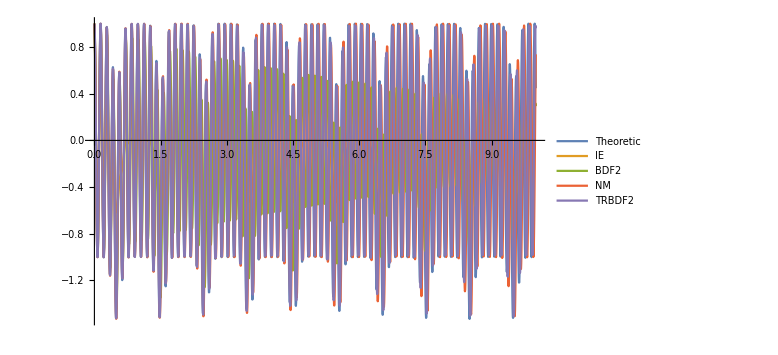

```mathematica
totalPlots = ListLinePlot[{theoList, IEtimeα, BDF2timeα, NMtimeα, TRBDF2timeα}, PlotRange->All, PlotLegends->{"Theoretic", "IE", "BDF2", "NM","TRBDF2"}, ImageSize->Large]
```

```mathematica
Export[filePrefex<>"_total_plots.png", totalPlots];
```

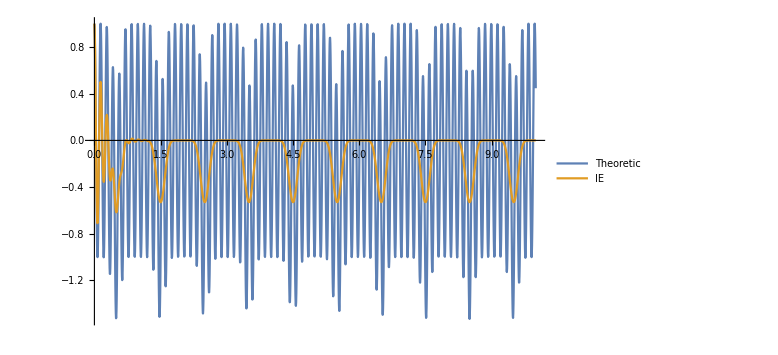

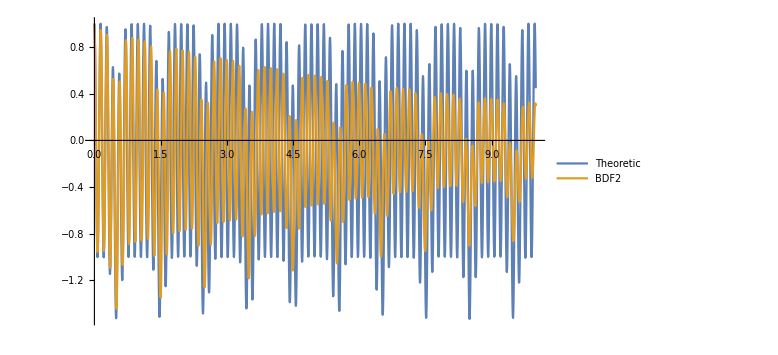

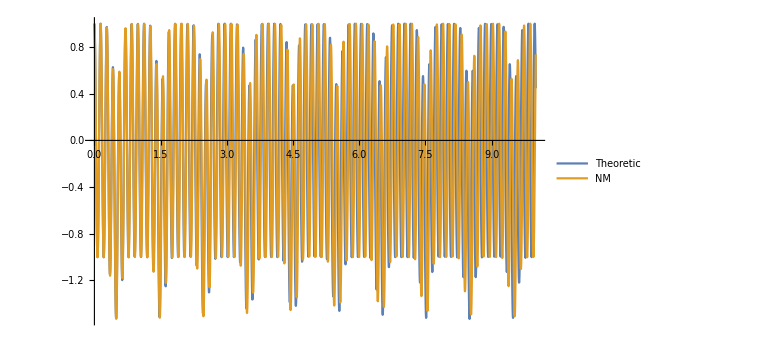

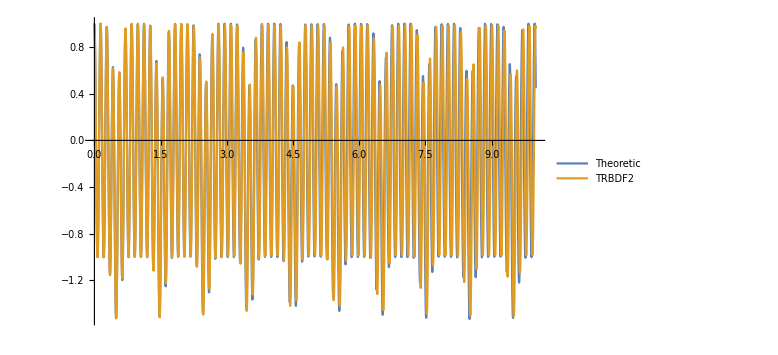

```mathematica
IEPlots = ListLinePlot[{theoList, IEtimeα}, PlotRange->All, PlotLegends->{"Theoretic", "IE"}, ImageSize->Large]
Export[filePrefex<>"_IE_plots.png", IEPlots];
BDF2Plots = ListLinePlot[{theoList, BDF2timeα}, PlotRange->All, PlotLegends->{"Theoretic", "BDF2"}, ImageSize->Large]
Export[filePrefex<>"_BDF2_plots.png", BDF2Plots];
NMPlots = ListLinePlot[{theoList, NMtimeα}, PlotRange->All, PlotLegends->{"Theoretic", "NM"}, ImageSize->Large]
Export[filePrefex<>"_NM_plots.png", NMPlots];
TRBDF2Plots = ListLinePlot[{theoList, TRBDF2timeα}, PlotRange->All, PlotLegends->{"Theoretic","TRBDF2"}, ImageSize->Large]
Export[filePrefex<>"_TRBDF2_plots.png", TRBDF2Plots];
```